Задача 4. Дадена е задачата y’=y-(2+a)sinx, y(b)=a+b, x∈[b; b+0.5], където a=0, b=3

а) Да се намери точното решение на задачата.

Търсим общо решение :

```mathematica
Clear[x,y]
DSolve[y'[x]==y[x]- 2Sin[x], y[x],x]
```

{{y[x]→ⅇ^x C[1]+Cos[x]+Sin[x]}}

Търсим точно решение :

```mathematica
Clear[x,y]
DSolve[{y'[x]==y[x]- 2Sin[x], y[3]==3}, y[x],x]
```

{{y[x]→(3 ⅇ^x-ⅇ^x Cos[3]+ⅇ^3 Cos[x]-ⅇ^x Sin[3]+ⅇ^3 Sin[x])/ⅇ^3}}

Визуализация на точното решение:

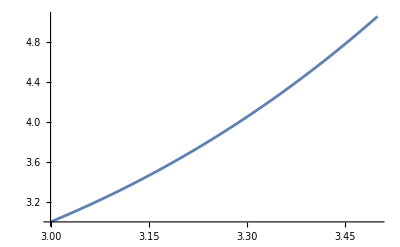

```mathematica
yt[x_]:=(3 ⅇ^x-ⅇ^x Cos[3]+ⅇ^3 Cos[x]-ⅇ^x Sin[3]+ⅇ^3 Sin[x])/ⅇ^3
Plot[yt[x], {x, 3,3.5}]
```

б) По метод на Рунге - Кута (1,1) да се реши приближено задачата със стъпка h=0.025. Запишете резултатите в таблица. Сравнете с точното решение.

#### Метод на Рунге-Кута (1, 1)

Мрежата е с n = 20. и стъпка h = 0.025

Теоретичната локална  грешка е 0.000015625

Теоретичната глобална грешка е 0.000625

i = 0 x_i = 3. y_i = 3. k1 = 0.067944 k2 = 0.0708822 y_точно = 3. истинска грешка = 0.

i = 1 x_i = 3.025 y_i = 3.06941 k1 = 0.0709189 k2 = 0.0739351 y_точно = 3.06943 истинска грешка = 0.0000119798

i = 2 x_i = 3.05 y_i = 3.14184 k1 = 0.0739728 k2 = 0.0770681 y_точно = 3.14186 истинска грешка = 0.0000246554

i = 3 x_i = 3.075 y_i = 3.21736 k1 = 0.0771068 k2 = 0.0802827 y_точно = 3.2174 истинска грешка = 0.0000380496

i = 4 x_i = 3.1 y_i = 3.29606 k1 = 0.0803223 k2 = 0.0835798 y_точно = 3.29611 истинска грешка = 0.0000521859

i = 5 x_i = 3.125 y_i = 3.37801 k1 = 0.0836206 k2 = 0.086961 y_точно = 3.37807 истинска грешка = 0.0000670884

i = 6 x_i = 3.15 y_i = 3.4633 k1 = 0.0870028 k2 = 0.0904276 y_точно = 3.46338 истинска грешка = 0.000082782

i = 7 x_i = 3.175 y_i = 3.55201 k1 = 0.0904704 k2 = 0.0939808 y_точно = 3.55211 истинска грешка = 0.0000992922

i = 8 x_i = 3.2 y_i = 3.64424 k1 = 0.0940247 k2 = 0.0976221 y_точно = 3.64435 истинска грешка = 0.000116645

i = 9 x_i = 3.225 y_i = 3.74006 k1 = 0.0976671 k2 = 0.101353 y_точно = 3.7402 истинска грешка = 0.000134869

i = 10 x_i = 3.25 y_i = 3.83957 k1 = 0.101399 k2 = 0.105175 y_точно = 3.83973 истинска грешка = 0.00015399

i = 11 x_i = 3.275 y_i = 3.94286 k1 = 0.105222 k2 = 0.109089 y_точно = 3.94303 истинска грешка = 0.000174037

i = 12 x_i = 3.3 y_i = 4.05001 k1 = 0.109138 k2 = 0.113098 y_точно = 4.05021 истинска грешка = 0.000195041

i = 13 x_i = 3.325 y_i = 4.16113 k1 = 0.113147 k2 = 0.117202 y_точно = 4.16135 истинска грешка = 0.000217032

i = 14 x_i = 3.35 y_i = 4.27631 k1 = 0.117253 k2 = 0.121404 y_точно = 4.27655 истинска грешка = 0.00024004

i = 15 x_i = 3.375 y_i = 4.39563 k1 = 0.121456 k2 = 0.125704 y_точно = 4.3959 истинска грешка = 0.000264098

i = 16 x_i = 3.4 y_i = 4.51921 k1 = 0.125757 k2 = 0.130106 y_точно = 4.5195 истинска грешка = 0.00028924

i = 17 x_i = 3.425 y_i = 4.64715 k1 = 0.13016 k2 = 0.13461 y_точно = 4.64746 истинска грешка = 0.0003155

i = 18 x_i = 3.45 y_i = 4.77953 k1 = 0.134665 k2 = 0.139218 y_точно = 4.77987 истинска грешка = 0.000342912

i = 19 x_i = 3.475 y_i = 4.91647 k1 = 0.139275 k2 = 0.143933 y_точно = 4.91684 истинска грешка = 0.000371514

i = 20 x_i = 3.5 y_i = 5.05808 k1 = 0.143991 k2 = 0.148756 y_точно = 5.05848 истинска грешка = 0.000401342

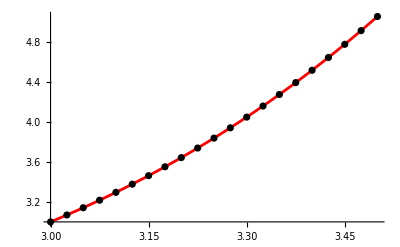

```mathematica
(*въвеждаме условието на задачата*)
a = 3.; b = 3.5;
x = a;
y = 3.;
points = {{x,y}};
f[x_,y_]:=y - 2Sin[x]
(*точно решение*)
yt[x_]:=(3 ⅇ^x-ⅇ^x Cos[3]+ⅇ^3 Cos[x]-ⅇ^x Sin[3]+ⅇ^3 Sin[x])/ⅇ^3
(*съставяме мрежата*)
h=0.025; n = (b-a)/h;
Print["Мрежата е с n = ", n, " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална  грешка е ", h^3]
Print["Теоретичната глобална грешка е ", h^2]
(*намираме неизвестните стойности за Subscript[y, i]*)
For[i = 0, i<= n, i++,
k1 = h*f[x,y];
k2 = h*f[x+h,y+k1];
Print["i = ", i, " x_i = ",x, " y_i = ",y, " k1 = ",k1," k2 = ",k2,  " y_(:0442:043e:0447:043d:043e) = ", yt[x], " истинска грешка = ", Abs[y-yt[x]]];
y = y+1/2(k1+k2);
x=x+h;
AppendTo[points,{x,y}]
]
(*визуализация на резултатите*)
gryt = Plot[yt[x],{x,a,b}, PlotStyle->Red];
grp = ListPlot[points, PlotStyle->Black];
Show[gryt,grp]
```

в) Каква е теоретичната грешка на полученото приближено решение?

Отговор: Да се препишат теоретичната локална и глобална грешка.

г) Каква би била точността при използване на модифицирания метод на Ойлер за поставената задача със същата стъпка? Направете сравнение между двата метода.

#### Модифициран метод на Ойлер

Мрежата е с n = 20. и стъпка h = 0.025

Теоретичната локална  грешка е 0.000015625

Теоретичната глобална грешка е 0.000625

i = 0 x_i = 3. y_i = 3. f_i = 2.71776 x_(i + 1/2) = 3.0125 y_(i + 1/2) = 3.03397 f_(i + 1/2) = 2.7765 y_точно = 3. истинска грешка = 0.

i = 1 x_i = 3.025 y_i = 3.06941 f_i = 2.83676 x_(i + 1/2) = 3.0375 y_(i + 1/2) = 3.10487 f_(i + 1/2) = 2.89706 y_точно = 3.06943 истинска грешка = 0.0000124826

i = 2 x_i = 3.05 y_i = 3.14184 f_i = 2.95891 x_(i + 1/2) = 3.0625 y_(i + 1/2) = 3.17883 f_(i + 1/2) = 3.02081 y_точно = 3.14186 истинска грешка = 0.0000255768

i = 3 x_i = 3.075 y_i = 3.21736 f_i = 3.08427 x_(i + 1/2) = 3.0875 y_(i + 1/2) = 3.25591 f_(i + 1/2) = 3.14778 y_точно = 3.2174 истинска грешка = 0.000039303

i = 4 x_i = 3.1 y_i = 3.29605 f_i = 3.21289 x_(i + 1/2) = 3.1125 y_(i + 1/2) = 3.33621 f_(i + 1/2) = 3.27804 y_точно = 3.29611 истинска грешка = 0.0000536822

i = 5 x_i = 3.125 y_i = 3.378 f_i = 3.34482 x_(i + 1/2) = 3.1375 y_(i + 1/2) = 3.41981 f_(i + 1/2) = 3.41163 y_точно = 3.37807 истинска грешка = 0.0000687362

i = 6 x_i = 3.15 y_i = 3.4633 f_i = 3.48011 x_(i + 1/2) = 3.1625 y_(i + 1/2) = 3.5068 f_(i + 1/2) = 3.54861 y_точно = 3.46338 истинска грешка = 0.0000844875

i = 7 x_i = 3.175 y_i = 3.55201 f_i = 3.61881 x_(i + 1/2) = 3.1875 y_(i + 1/2) = 3.59725 f_(i + 1/2) = 3.68903 y_точно = 3.55211 истинска грешка = 0.000100959

i = 8 x_i = 3.2 y_i = 3.64424 f_i = 3.76098 x_(i + 1/2) = 3.2125 y_(i + 1/2) = 3.69125 f_(i + 1/2) = 3.83294 y_точно = 3.64435 истинска грешка = 0.000118175

i = 9 x_i = 3.225 y_i = 3.74006 f_i = 3.90668 x_(i + 1/2) = 3.2375 y_(i + 1/2) = 3.78889 f_(i + 1/2) = 3.98041 y_точно = 3.7402 истинска грешка = 0.00013616

i = 10 x_i = 3.25 y_i = 3.83957 f_i = 4.05596 x_(i + 1/2) = 3.2625 y_(i + 1/2) = 3.89027 f_(i + 1/2) = 4.1315 y_точно = 3.83973 истинска грешка = 0.00015494

i = 11 x_i = 3.275 y_i = 3.94286 f_i = 4.20888 x_(i + 1/2) = 3.2875 y_(i + 1/2) = 3.99547 f_(i + 1/2) = 4.28625 y_точно = 3.94303 истинска грешка = 0.000174541

i = 12 x_i = 3.3 y_i = 4.05001 f_i = 4.36551 x_(i + 1/2) = 3.3125 y_(i + 1/2) = 4.10458 f_(i + 1/2) = 4.44474 y_точно = 4.05021 истинска грешка = 0.000194989

i = 13 x_i = 3.325 y_i = 4.16113 f_i = 4.52589 x_(i + 1/2) = 3.3375 y_(i + 1/2) = 4.21771 f_(i + 1/2) = 4.60702 y_точно = 4.16135 истинска грешка = 0.000216314

i = 14 x_i = 3.35 y_i = 4.27631 f_i = 4.69011 x_(i + 1/2) = 3.3625 y_(i + 1/2) = 4.33493 f_(i + 1/2) = 4.77316 y_точно = 4.27655 истинска грешка = 0.000238544

i = 15 x_i = 3.375 y_i = 4.39564 f_i = 4.85822 x_(i + 1/2) = 3.3875 y_(i + 1/2) = 4.45636 f_(i + 1/2) = 4.94324 y_точно = 4.3959 истинска грешка = 0.000261709

i = 16 x_i = 3.4 y_i = 4.51922 f_i = 5.0303 x_(i + 1/2) = 3.4125 y_(i + 1/2) = 4.5821 f_(i + 1/2) = 5.11731 y_точно = 4.5195 истинска грешка = 0.000285839

i = 17 x_i = 3.425 y_i = 4.64715 f_i = 5.20641 x_(i + 1/2) = 3.4375 y_(i + 1/2) = 4.71223 f_(i + 1/2) = 5.29545 y_точно = 4.64746 истинска грешка = 0.000310967

i = 18 x_i = 3.45 y_i = 4.77954 f_i = 5.38662 x_(i + 1/2) = 3.4625 y_(i + 1/2) = 4.84687 f_(i + 1/2) = 5.47772 y_точно = 4.77987 истинска грешка = 0.000337126

i = 19 x_i = 3.475 y_i = 4.91648 f_i = 5.57101 x_(i + 1/2) = 3.4875 y_(i + 1/2) = 4.98612 f_(i + 1/2) = 5.66422 y_точно = 4.91684 истинска грешка = 0.000364349

i = 20 x_i = 3.5 y_i = 5.05809 f_i = 5.75965 x_(i + 1/2) = 3.5125 y_(i + 1/2) = 5.13008 f_(i + 1/2) = 5.855 y_точно = 5.05848 истинска грешка = 0.000392672

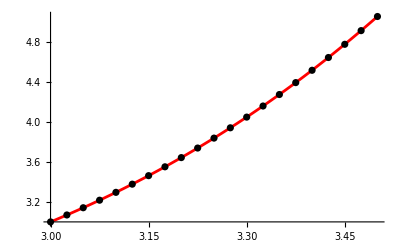

```mathematica
(*въвеждаме условието на задачата*)
a = 3.; b = 3.5;
x = a;
y = 3.;
points = {{x,y}};
f[x_,y_]:=y - 2Sin[x]
(*точно решение*)
yt[x_]:=(3 ⅇ^x-ⅇ^x Cos[3]+ⅇ^3 Cos[x]-ⅇ^x Sin[3]+ⅇ^3 Sin[x])/ⅇ^3
(*съставяме мрежата*)
h=0.025; n = (b-a)/h;
Print["Мрежата е с n = ", n, " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална  грешка е ", h^3]
Print["Теоретичната глобална грешка е ", h^2]
(*намираме неизвестните стойности за Subscript[y, i]*)
For[i = 0, i<= n, i++,
x12 = x+h/2;
y12 = y +h/2*f[x,y];
Print["i = ", i, " x_i = ",x, " y_i = ",y, " f_i = ",f[x,y], " x_(i + 1/2) = ",x12, " y_(i + 1/2) = ",y12, " f_(i + 1/2) = ",f[x12,y12], " y_(:0442:043e:0447:043d:043e) = ", yt[x], " истинска грешка = ", Abs[y-yt[x]]];
y = y+h*f[x12,y12];
x=x+h;
AppendTo[points,{x,y}]
]
(*визуализация на резултатите*)
gryt = Plot[yt[x],{x,a,b}, PlotStyle->Red];
grp = ListPlot[points, PlotStyle->Black];
Show[gryt,grp]
```

Отговор: При 20 итерации със същата стъпка с метода на Рунге - Кута (1,1) приближеното решение е 5.05808 с грешка 0.000401342. При модифицирания метод на Ойлер приближеното решение е 5.05809 с грешка  0.000392672. Следователно модифицираният метод на Ойлер е по-точен.